```mathematica
(*zad 1*) 
Solve[{{1, 2, 0}, {-1, 1, 0}, {0, 1, 2}}.{x, y, z} == {3, 1, 3}, {x, y, z}]
```

{{x→1/3,y→4/3,z→5/6}}

```mathematica
(*zad 2*) 
Solve[{{1, -2, 3}, {2, 3, -1}}.{x, y, z} == {1, 5}, {x, y, z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→16/7-x,z→13/7-x}}

```mathematica
(*zad 3*)
{Limit[e^x/(x^3 + x^2), x -> Infinity],
Limit[(e^(2/x))/(x + 1), x -> 1, Direction -> "FromAbove"],
Limit[(e^(2/x))/(x - 1), x -> 1, Direction -> "FromBelow"],
Integrate[Sin[x]/x, {x, 0, Infinity}],
D[((x^3) Sin[x y])/((Cos[x^2 + x y])^5), {x, 2}, {y, 3}]}
```

```mathematica
(*zad 4*) 
DSolve[y'[x] == y[x] x, y[x], x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

```mathematica
(*zad 5*)
DSolve[{y'[x] == y[x] x, y[1] == 2}, y[x], x]
```

{{y[x]→2 ⅇ^(-1/2+x^2/2)}}

```mathematica
(*zad 6*) 
DSolve[2*D[y[x, t], x, x] + D[y[x, t], t] == 0, y[x, t], {x, t}]
```

DSolve::lpdeprtclr: General solution is not available for the given linear partial differential equation. Trying to build a particular solution.

{{y[x,t]→1/24 (24 C[1]+24 x C[2]-96 t C[3]+24 x^2 C[3]-288 t x C[4]+24 x^3 C[4]-48 t^2 C[8]+24 t x^2 C[8]-x^4 C[8])}}

```mathematica
(*zad 7*) 
Normal[Series[Exp[x], {x, 0, 5}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

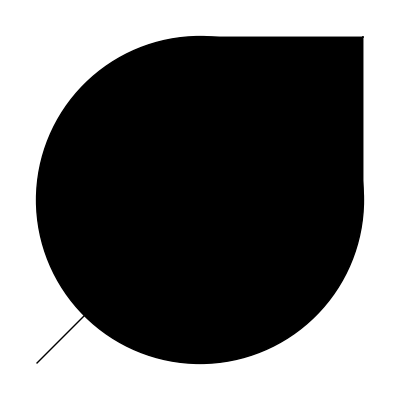

```mathematica
(*zad 8*)
Graphics[{Circle[], Disk[], Arrow[{{0, 0}, {1, 1}}], Line[{{-1, -1}, {1, 1}}], Rectangle[]}]
```

```mathematica
(*zad 9*)
f[x_] := Piecewise[{{3, x ≤ 0}, {x^2 + 1, x > 0}}];
Plot[f[x], {x, -2, 2}, PlotStyle -> {Thick, Purple}, Exclusions -> None, ExclusionsStyle -> {Red, PointSize[0.02]}]
```

-Graphics-